```mathematica
n=4*10^3;
e=4.8*10^-10;
eps0=8.85*10^-12;
m=9.1*10^-28;
c=3*10^10;
pi=3.1416;
h=1.05*10^-27;
kB=1.380649*10^-16;
T=2000;
t=1;
C1=2;
C2=1;
x=1;
Gx=C1+C2/x^2;
Gxp=(-2C2)/x^3;
z=1;
wp=((4*pi*n*e^2)/m)^(1/2)
```

3.56743×10^6

```mathematica
v=Sqrt[(2*kB*T)/m]
```

2.46349×10^7

```mathematica
lemda=v/wp
```

6.9055

```mathematica
beta=1/lemda
```

0.144812

```mathematica
w=Sqrt[beta^2*c^2+wp^2]
```

4.34437×10^9

```mathematica
eps=1-wp^2/w^2
```

0.999999

```mathematica
k=Sqrt[√2(w^2/c^2*eps- beta^2)]
```

3.13258×10^-9

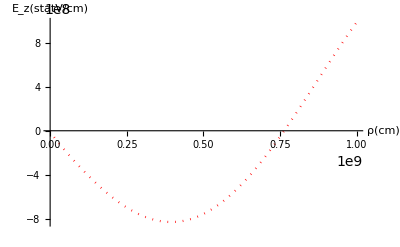

```mathematica
sigma1=0.6;
p1=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma1)]],{rho,0.06,1000000000},PlotStyle->{Dotted,Red},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

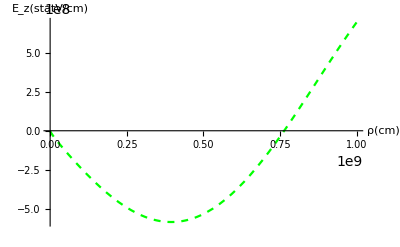

```mathematica
sigma2=0.8;
p2=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma2)]],{rho,0.06,1000000000},PlotStyle->{Dashed,Green},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

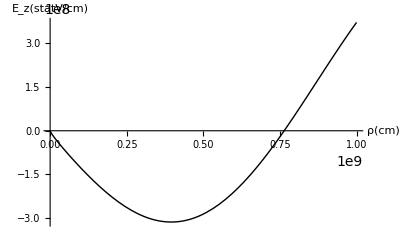

```mathematica
sigma3=1.0;
p3=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma3)]],{rho,0.06,1000000000},PlotStyle->{Thick,Black},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

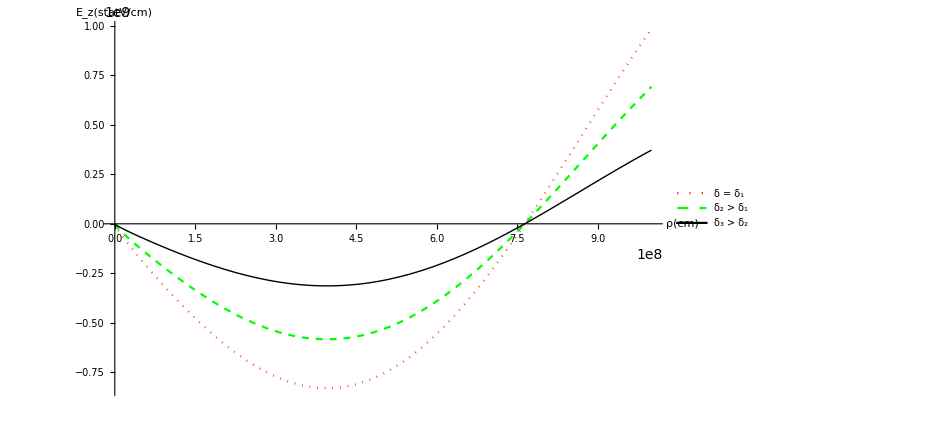

```mathematica
C1=Show[p1,p2,p3];

legendLabels={"δ = δ_1","δ_2 > δ_1","δ_3 > δ_2"};
lineStyles={Dotted,Dashed,Solid};
directives={Directive[Red,Dotted],Directive[Green,Dashed],Directive[Black,Solid]};
Legended[C1,Placed[LineLegend[directives,legendLabels,LegendLayout->"Column"],{0.4,0.80}]]
```

```mathematica
Export["F:\\Plots_w.r.t_rho\\Space_Plasma\\Plots\\Ez\\panel_b.png",%646,"PNG"]
```

F:\Plots_w.r.t_rho\Space_Plasma\Plots\Ez\panel_b.png

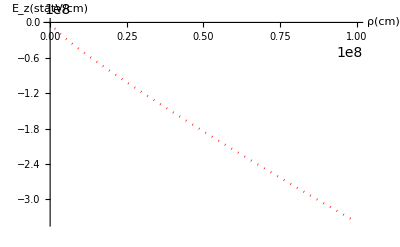

```mathematica
sigma01=0.6;
p01=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma01)]],{rho,0.06,100000000},PlotStyle->{Dotted,Red},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

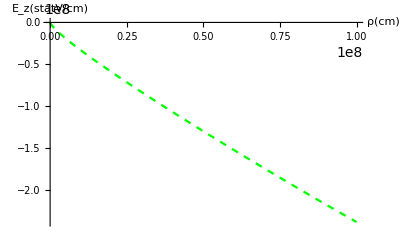

```mathematica
sigma02=0.8;
p02=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma02)]],{rho,0.06,100000000},PlotStyle->{Dashed,Green},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

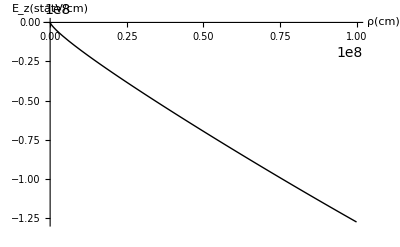

```mathematica
sigma03=1.0;
p03=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma03)]],{rho,0.06,100000000},PlotStyle->{Thick,Black},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

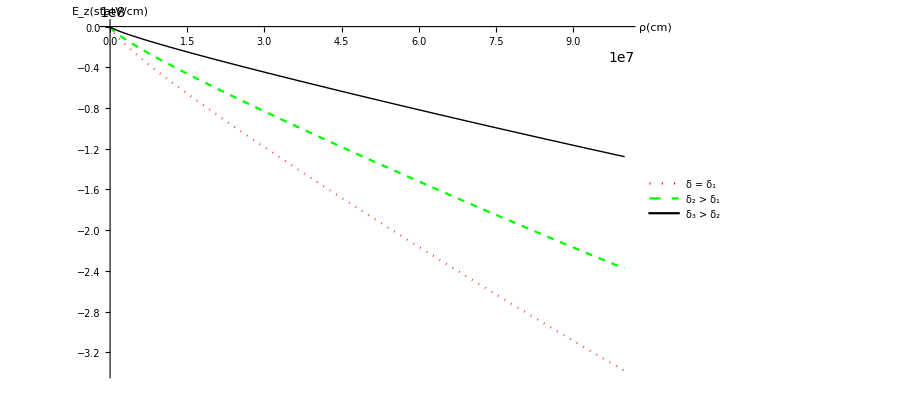

```mathematica
C2=Show[p01,p02,p03];

legendLabels={"δ = δ_1","δ_2 > δ_1","δ_3 > δ_2"};
lineStyles={Dotted,Dashed,Thick};
directives={Directive[Red,Dotted],Directive[Green,Dashed],Directive[Black,Thick]};
Legended[C2,Placed[LineLegend[directives,legendLabels,LegendLayout->"Column"],{0.3,0.4}]]
```

```mathematica
Export["F:\\Plots_w.r.t_rho\\Space_Plasma\\Plots\\Ez\\panel_a.png",%922,"PNG"]
```

F:\Plots_w.r.t_rho\Space_Plasma\Plots\Ez\panel_a.png

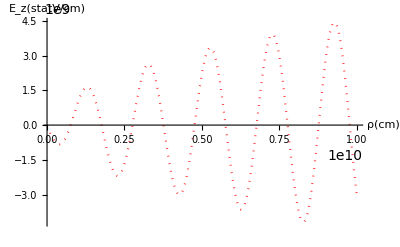

```mathematica
sigma001=0.6;
p001=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma001)]],{rho,100000000,10000000000},PlotStyle->{Dotted,Red},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

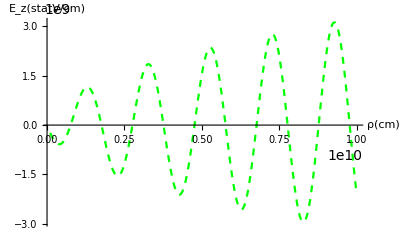

```mathematica
sigma002=0.8;
p002=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma002)]],{rho,100000000,10000000000},PlotStyle->{Dashed,Green},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

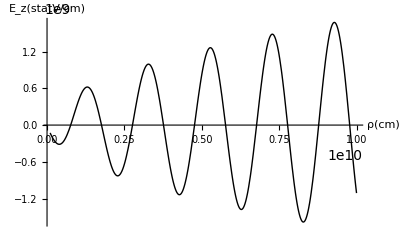

```mathematica
sigma003=1.0;
p003=Plot[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma003)]],{rho,100000000,10000000000},PlotStyle->{Thick,Black},AxesLabel->{"ρ(cm)","E_z(statV/cm)"},PlotRange->All]
```

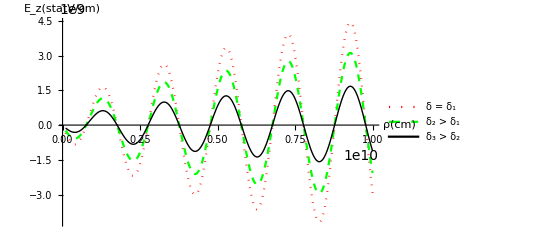

```mathematica
C3=Show[p001,p002,p003];

legendLabels={"δ = δ_1","δ_2 > δ_1","δ_3 > δ_2"};
lineStyles={Dotted,Dashed,Thick};
directives={Directive[Red,Dotted],Directive[Green,Dashed],Directive[Black,Thick]};
Legended[C3,Placed[LineLegend[directives,legendLabels,LegendLayout->"Column"],{0.2,0.80}]]
```

```mathematica
Export["F:\\Plots_w.r.t_rho\\Space_Plasma\\Plots\\Ez\\panel_b.png",%935,"PNG"]
```

F:\Plots_w.r.t_rho\Space_Plasma\Plots\Ez\panel_b.png

```mathematica
p11=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma1)]],{z,0,0.2},{rho,0.6,100000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->Function[{x,rho,z},Hue[.65 (1-z)]], PlotRange->All]
```

-Graphics3D-

```mathematica
p12=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma2)]],{z,0,0.2},{rho,0.6,100000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->Function[{x,rho,z},RGBColor[x,rho,0.]], PlotRange->All]
```

-Graphics3D-

```mathematica
p13=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma3)]],{z,0,0.2},{rho,0.6,100000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->"DarkRainbow",PlotStyle->Directive[Opacity[0.5],Red], PlotRange->All]
```

-Graphics3D-

```mathematica
C4=Show[p11,p12,p13]
```

-Graphics3D-

```mathematica
Export["F:\\Plots_w.r.t_rho\\Space_Plasma\\Plots\\Ez\\panel_d.png",C4,"PNG"]
```

F:\Plots_w.r.t_rho\Space_Plasma\Plots\Ez\panel_d.png

```mathematica
p110=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma1)]],{z,0,0.2},{rho,1000000,10000000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->Function[{x,rho,z},Hue[.65 (1-z)]], PlotRange->All]
```

-Graphics3D-

```mathematica
p120=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma2)]],{z,0,0.2},{rho,1000000,10000000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->Function[{x,rho,z},RGBColor[x,rho,0.]], PlotRange->All]
```

-Graphics3D-

```mathematica
p130=Plot3D[Re[(((x^2+(x^4+rho^4)^(1/2))^2-4*x^4)^(1/2))/rho *(BesselJ[1/4,rho*k]+BesselJ[-1/4,rho*k])*Gx*Exp[ⅈ(w*t-beta*z+sigma3)]],{z,0,0.2},{rho,1000000,10000000000},AxesLabel->{"z(cm)","ρ(cm)","E_z(statV/cm)"},ColorFunction->"DarkRainbow",PlotStyle->Directive[Opacity[0.5],Red], PlotRange->All]
```

-Graphics3D-

```mathematica
C5=Show[p110,p120,p130]
```

-Graphics3D-